```mathematica
Taylor展开的逼近效果
```

```mathematica
1、求给定函数的Taylor展开式（带Peano余项）
```

```mathematica
Series[Sin[x],{x,0,20}]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880-x^11/39916800+x^13/6227020800-x^15/1307674368000+x^17/355687428096000-x^19/121645100408832000+O[x]^21

```mathematica
2、不同阶数的展开式的逼近效果对比
```

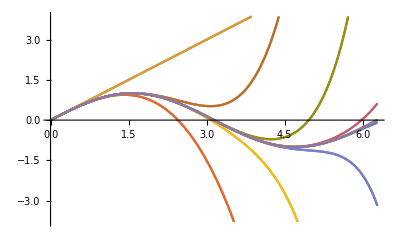

```mathematica
Plot[Evaluate[Table[Normal[Series[Sin[x],{x,0,n}]],{n,20}]],{x,0,2Pi}]
```

```mathematica
3、动态的逼近过程
```

```mathematica
y=sin(x)
```

```mathematica
Manipulate[Plot[{Sin[x],Evaluate[Table[Normal[Series[Sin[x],{x,0,m}]],{m,1,n}]]},{x,-Pi,5Pi},Filling->{1->{n}},PlotRange->4],{n,1,31,2}]
```

#### y=e^x

```mathematica
Manipulate[Plot[{E^x,Evaluate[Table[Normal[Series[E^x,{x,0,m}]],{m,1,n}]]},{x,-10,3},Filling->{1->{n}},PlotRange->8],{n,1,31,1}]
```

```mathematica
y=ln(x+1)
```

```mathematica
Manipulate[Plot[{Log[x+1],Evaluate[Table[Normal[Series[Log[x+1],{x,0,m}]],{m,1,n}]]},{x,-1,4},Filling->{1->{n}},PlotRange->4],{n,1,31,1}]
```

```mathematica
y=√(1+x)
```

```mathematica
Manipulate[Plot[{Sqrt[1+x],Evaluate[Table[Normal[Series[Sqrt[1+x],{x,0,m}]],{m,1,n}]]},{x,-1,2},Filling->{1->{n}},PlotRange->2],{n,1,31,1}]
```

```mathematica
y=tan(x)
```

```mathematica
Manipulate[Plot[{Tan[x],Evaluate[Table[Normal[Series[Tan[x],{x,0,m}]],{m,1,n}]]},{x,-2,2},Filling->{1->{n}},PlotRange->10],{n,1,31,1}]
```

```mathematica
y=arctan(x)
```

```mathematica
Manipulate[Plot[{ArcTan[x],Evaluate[Table[Normal[Series[ArcTan[x],{x,0,m}]],{m,1,n}]]},{x,-10,10},Filling->{1->{n}},PlotRange->3],{n,1,31,1}]
```